```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
```

### Basic Examples

Cluster one-dimensional data:

```mathematica
PrincipalAxisClustering[{{1},{2},{10},{12},{3},{1},{13},{25}}]
```

{{{1},{2},{3},{1}},{{10},{12},{13},{25}}}

Find exactly four clusters:

```mathematica
PrincipalAxisClustering[{{1},{2},{10},{12},{3},{1},{13},{25}},4]
```

{{{1},{1}},{{2},{3}},{{10},{12},{13}},{{25}}}

Cluster vectors of real values:

```mathematica
PrincipalAxisClustering[{{2.5,3.1},{5.9,3.4},{10,15},{2.2,1.5},{100,7.5}}]
```

{{{2.5,3.1},{5.9,3.4},{10,15},{2.2,1.5}},{{100,7.5}}}

### Scope

Partition a 3D point cloud:

```mathematica
mesh=ResourceData["Stanford Bunny","MeshRegion"]
```

-Graphics-

```mathematica
ListPointPlot3D[PrincipalAxisClustering[RandomPoint[mesh,10000]],]
```

-Graphics3D-

Cluster high dimensional data:

```mathematica
points=RandomReal[1,{10000,100}];
First[AbsoluteTiming[PrincipalAxisClustering[points]]]
```

0.242309

### Options

#### Method

With the default setting of Method→Median, clusters are likely to span across gaps:

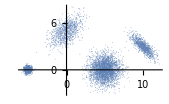

```mathematica
ListPlot[data=]
```

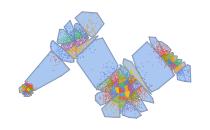

```mathematica
c1=PrincipalAxisClustering[data,Method->Median];
Show[RegionUnion@@ConvexHullMesh/@c1,ListPlot[c1]]
```

Using Method→Mean can improve separation:

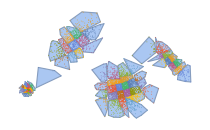

```mathematica
c2=PrincipalAxisClustering[data,Method->Mean];
Show[RegionUnion@@ConvexHullMesh/@c2,ListPlot[c2]]
```

However, Mean will tend to produce unbalanced cluster sizes compared to Median:

```mathematica
Length/@c1
```

{93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94,93,94,94,94}

```mathematica
Length/@c2
```

{42,57,66,86,57,54,76,58,77,95,89,65,69,65,43,5,35,44,48,29,34,46,57,32,75,98,126,112,114,131,91,80,131,161,180,203,132,137,223,167,159,199,182,111,200,189,170,130,39,45,43,39,28,47,23,46,73,102,121,129,132,121,102,80}

### Applications

Downsample a large point cloud by choosing nicely spaced representative points:

```mathematica
points=RandomPoint[ResourceData["Stanford Bunny","MeshRegion"],100000];
```

```mathematica
Graphics3D[Point[Median/@PrincipalAxisClustering[points,1000]]]
```

-Graphics3D-

Compare to random sampling:

```mathematica
Graphics3D[Point[RandomSample[points,1000]]]
```

-Graphics3D-

### Properties and Relations

The axis representing each cluster separation corresponds to the first component in PrincipalComponents:

```mathematica
points=N[Position[ImageData[-Graphics-],1,{2}]];
```

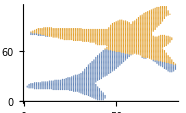

```mathematica
ListPlot[PrincipalAxisClustering[points,2]]
```

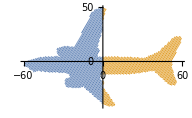

```mathematica
ListPlot[SplitBy[SortBy[PrincipalComponents[points],First],Negative@*First]]
```

The principal axis can be obtained from the Eigenvectors of the Covariance matrix:

```mathematica
pa=First[Eigenvectors[Covariance[points],UpTo[1]]]
```

{0.439069,0.898453}

Visualize the axis over the original data:

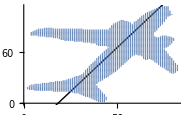

```mathematica
ListPlot[points,Epilog->Style[InfiniteLine[Mean[points],axis],Red]]
```

Projecting the standardized points onto the principal axis gives scalar values that indicate which cluster they belong to:

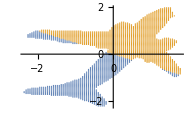

```mathematica
ListPlot[GatherBy[Standardize[points],Negative[#.pa]&]]
```

PrincipalAxisClustering finds clusters very quickly:

```mathematica
points=;
Dimensions[points]
```

{11169,2}

```mathematica
First@RepeatedTiming[c1=PrincipalAxisClustering[points,16]]
```

0.0169336

Compare to FindClusters:

```mathematica
First@RepeatedTiming[c2=FindClusters[points,16]]
```

6.54586

PrincipalAxisClustering gives clusters that better represent the local point cloud density:

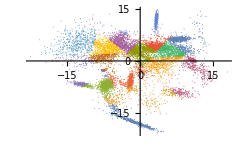

```mathematica
ListPlot[c1]
```

FindClusters represents better separation of the data:

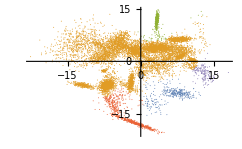

```mathematica
ListPlot[c2]
```

PrincipalAxisClustering partitions points into non-overlapping convex regions:

```mathematica
clusters=PrincipalAxisClustering[RandomVariate[BinormalDistribution[0],20000]];
```

```mathematica
Show[RegionUnion@@ConvexHullMesh/@clusters,ListPlot[clusters],PlotRange->2]
```

-Graphics-

The number of clusters locally scales with the point cloud density:

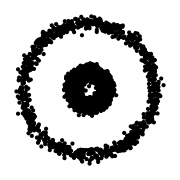

```mathematica
Graphics[Point[points=]]
```

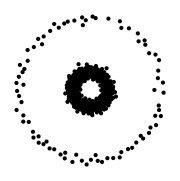

```mathematica
Graphics[Point[Median/@PrincipalAxisClustering[pts,500]]]
```

### Possible Issues

If the number of requested clusters is not a power of two, then cluster sizes will not be well balanced:

```mathematica
points=RandomReal[1,{100,2}];
```

```mathematica
Length/@PrincipalAxisClustering[points,5]
```

{12,13,25,25,25}

```mathematica
Length/@PrincipalAxisClustering[points,8]
```

{12,13,12,13,12,13,12,13}

### Neat Examples

Visualize the recursive nature of the clustering:

```mathematica
data=RandomReal[{-1,1},{10^4,2}];
```

```mathematica
plots=Table[ListPlot[PrincipalAxisClustering[data,2^n],],{n,0,5}];
```

```mathematica
GraphicsGrid[Partition[plots,3]]
```

-Graphics-

Partition a point cloud into clusters:

```mathematica
points=;
ListPlot[clusters=PrincipalAxisClustering[points]]
```

-Graphics-

Remove some outliers from each cluster:

```mathematica
filterOutliers[cluster_,q_]:=
Module[{m,d,t},
m=Mean[cluster];
d=Norm[#-m]&/@cluster;
t=Quantile[d,1-q];
Pick[cluster,#<t&/@d]
];
```

```mathematica
filtered=filterOutliers[#,.3]&/@clusters;
```

```mathematica
expand[cluster_,s_]:=
With[{m=Mean[cluster]},
m+s(#-m)&/@cluster
];
```

Construct a parameterized topological representation of the point cloud:

```mathematica
Manipulate[Show[RegionUnion@@(ConvexHullMesh[expand[#,e]]&/@filtered),ListPlot[points]],{{e,1},0.01,5}]
```

-Graphics-